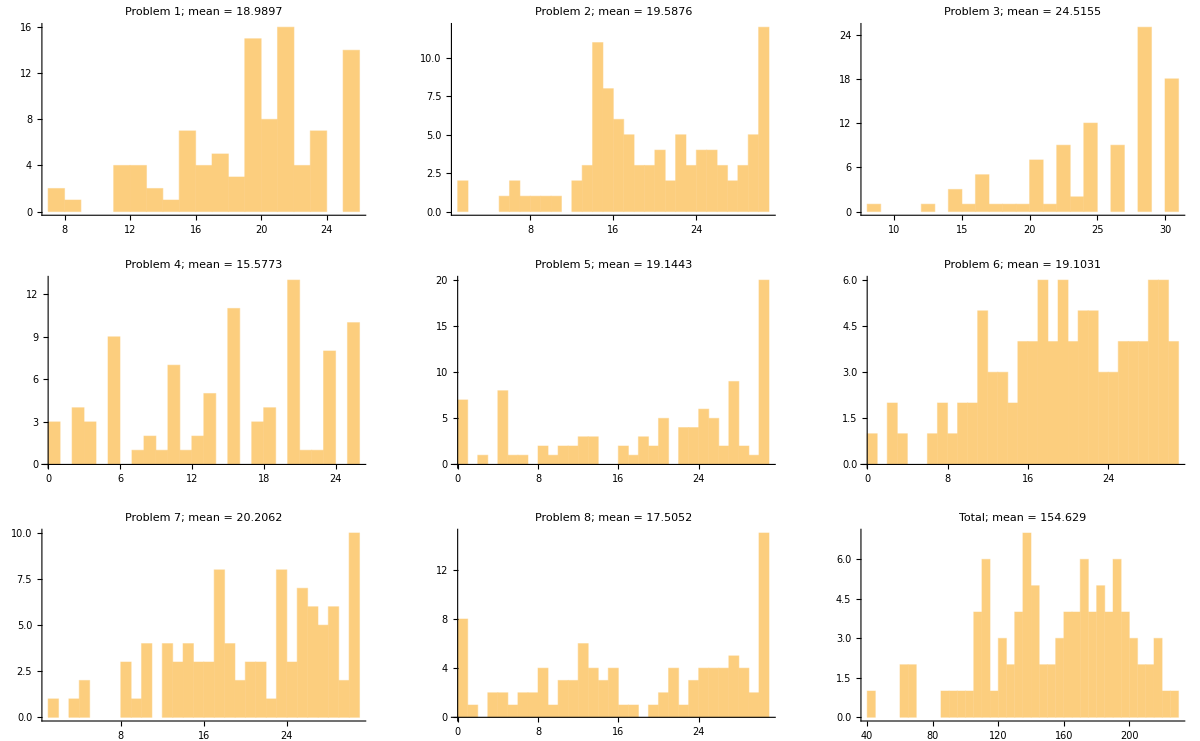

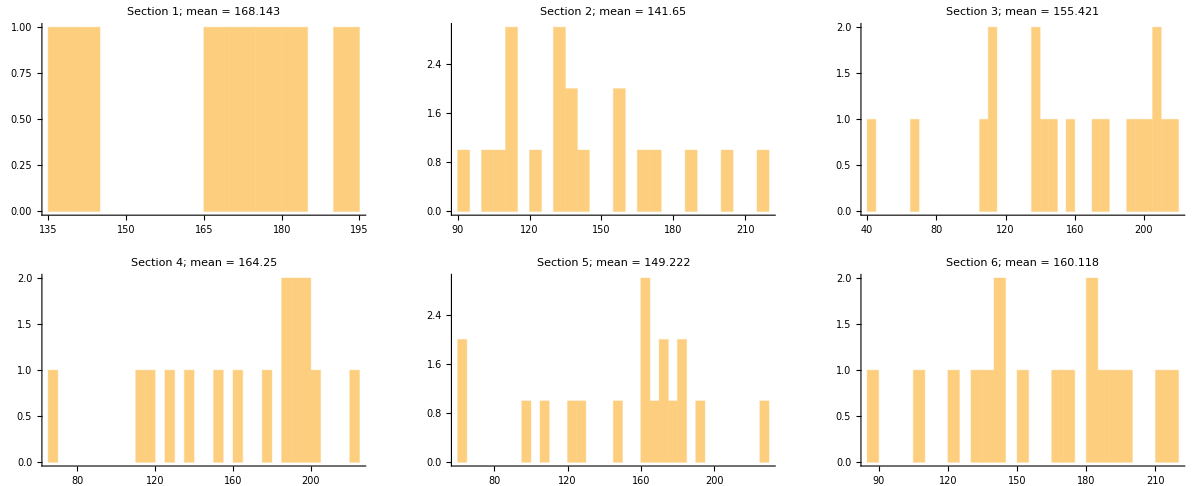

```mathematica
(*GradeReport.nb revision 2016/12/14. Written and maintained by Charles Hussong chussong@jhu.edu. Find most recent version at github.com/chussong/teaching-tools/*)

(*Takes grade data in a spreadsheet and outputs histograms of students' performance on each problem and on the overall exam. Expected data format is: names in first two columns, then each student's section number in third column, then each problem's score in subsequent columns. The top row is expected to be used for column labels and is not read.*)

(*Students whose problem scores are all blank will be treated as bad data and removed. Students whose scores are partially blank will have the blanks changed to 0s. Rows containing things that aren't #.0 #.5 or #.25 in cells which are supposed to contain problem scores will be excised on the assumption that they are calculated statistical columns. No other data alterations are made.*)

ClearAll["Global`*"];
maxpoints={25,30,30,25,30,30,30,30};  (*maximum points for each problem*)
totalBinSize=5; (*bin size for total-score histograms*)
dataname="finalgrades.xlsx";
exportName="finalreport.pdf";
SetDirectory[NotebookDirectory[]<>"../Exams/final/"]; (*Directory containing the data to be read. Report will also be exported here. NotebookDirectory[] is just where this notebook is.*)

(*--------------------------------------------------------------------------*)

(*Data reading and cleanup*)
problems=Length@maxpoints;
maxpoints=Append[Total@maxpoints]@maxpoints;
blankCondition={_,_,_};
Do[blankCondition=Append[""]@blankCondition,problems];
hist=ConstantArray[0,problems+1];
data=Import[dataname,"Data"];
If[Length@data==1,data=data[[1]]];
data=Delete[1]@data;
students=0;
currentRow=1;
While[currentRow≤Length@data,
If[MatchQ[blankCondition]@Take[data[[currentRow]],problems+3],
data=Delete[data,currentRow];
Continue[];
];
If[Norm[Take[data[[currentRow]],{4,problems+3}]*4-Round[Take[data[[currentRow]],{4,problems+3}]*4]]>0.01,
data=Delete[data,currentRow];
Continue[];
];
students++;
currentRow++;
];
Do[data[[i]]=Take[data[[i]],{1,problems+3}],{i,1,students}];
data=Replace[data,""->0,∞];
Do[data[[i]]=Append[Total@Take[data[[i]],{4,problems+3}]]@data[[i]],{i,1,students}];

(*Whole-class analysis and visualization*)
classMean=Mean@data[[All,problems+4]];
classMean=N[classMean,IntegerLength@Round@classMean+2];
classStDev=StandardDeviation@data[[All,problems+4]];
classStDev=N[classStDev,IntegerLength@Round@classStDev+2];
classMedian=Median@data[[All,problems+4]];
maxCount=ConstantArray[0,problems+1];
Do[maxCount[[i]]=Max@BinCounts[data[[All,3+i]],1];,{i,1,problems}];
maxCount[[problems+1]]=Max@BinCounts[data[[All,4+problems]],totalBinSize];
Do[
hist[[i]]=Histogram[data[[All,3+i]],{0,maxpoints[[i]]+1,1},PlotLabel->"Problem "<>ToString[i]<>"; mean = "<>ToString@N[Mean@data[[All,3+i]],4],AxesOrigin->0,PlotRange->Max@maxCount];
,{i,1,problems}]
totalEndpoint=maxpoints[[problems+1]]-Mod[maxpoints[[problems+1]],totalBinSize];
hist[[problems+1]]=Histogram[data[[All,problems+4]],{0,totalEndpoint+1,totalBinSize},PlotLabel->"Total; mean = "<>ToString@N[Mean@data[[All,4 + problems]],4],AxesOrigin->0,PlotRange-> Max@maxCount];
columns=Ceiling@Sqrt@(problems+1);
rows=Ceiling@((problems+1)/columns);
histGrid=ConstantArray["",{rows,columns}];
pos={1,1};
Do[histGrid[[pos[[1]],pos[[2]]]]=hist[[i]];
pos[[2]]++;
If[pos[[2]]>columns,
pos[[1]]++;
pos[[2]]=1;
];
,{i,1,problems+1}];
Print[GraphicsGrid[histGrid,ImageSize->Full]];

(*Section analysis and visualization*)
highestSection=Round@Max@data[[All,3]];
If[highestSection>0,
secData=Table[{},highestSection];secHist=ConstantArray[0,highestSection];
sectionMeans=ConstantArray[0,highestSection];
sectionMaxCount=ConstantArray[0,highestSection];
scoreVectors=data[[All,Range[3,problems+4]]];
Do[If[scoreVectors[[row]][[1]]>0,
secData[[scoreVectors[[row]][[1]]]]=Append[secData[[scoreVectors[[row]][[1]]]],scoreVectors[[row]][[Range[2,problems+2]]]];
];
,{row,1,students}];
Do[sectionMaxCount[[i]]=Max@BinCounts[secData[[i]][[All,problems+1]],totalBinSize];,{i,1,highestSection}];
Do[If[sectionMaxCount[[i]]==0,Continue[]];
sectionMeans[[i]]=Mean@secData[[i]][[All,problems+1]];
sectionMeans[[i]]=N[sectionMeans[[i]],IntegerLength@Round@sectionMeans[[i]]+2];
secHist[[i]]=Histogram[secData[[i]][[All,problems+1]],{0,totalEndpoint,totalBinSize},PlotRange->Max@sectionMaxCount,PlotLabel-> "Section "<>ToString[i]<>"; mean = "<>ToString[sectionMeans[[i]]]];
,{i,1,highestSection}];
secColumns=Ceiling@Sqrt@(highestSection-Count[sectionMaxCount,0]);
secRows=Ceiling@((highestSection-Count[sectionMaxCount,0])/secColumns);
secHistGrid=ConstantArray["",{secRows,secColumns}];
pos={1,1};
Do[If[sectionMaxCount[[i]]==0,Continue[]];
secHistGrid[[pos[[1]],pos[[2]]]]=secHist[[i]];
pos[[2]]++;
If[pos[[2]]>secColumns,
pos[[1]]++;
pos[[2]]=1;
];
,{i,1,highestSection}];
Print[GraphicsGrid[secHistGrid,ImageSize->Full]];
];

(*Create and export PDF report*)
report=CreateDocument[];
SetOptions[report,PageHeaders->{{None,None,None},{None,None,None}},PageFooters->{{None,None,None},{None,None,None}},PrintingOptions->{"PaperOrientation"->"Landscape","PrintingMargins"->{{20,20},{40,40}}}];
Paste[report,GraphicsGrid[histGrid,ImageSize->Full]];Paste[report,Framed["Additional statistics:\t\t St.Dev. = "<>ToString@classStDev<>"\t\t median = "<>ToString@N[classMedian] <> "\t\t" <> ToString[students] <> " students took this exam."]];
If[highestSection>0,Paste[report,GraphicsGrid[secHistGrid,ImageSize->Full]]];
Export[exportName,report];
NotebookClose[report];
```